```mathematica
(* Run KhBraids.nb first *)
```

```mathematica
Clear[MixedSpectralAnnularKh]
MixedSpectralAnnularKh[b_BR,r:(_Integer|_Rational)/;0≤r≤2]:=Module[{k,l},
k=Numerator[r/2];
l=Denominator[r/2]-k;
MixedSpectralAnnularKh[b,k,l]
]
MixedSpectralAnnularKh[b_BR,k_Integer,l_Integer]:=(*MixedSpectralAnnularKh[b,k,l]=*)Module[{result,ζ,β,γ,r,differentials,gradings},
r=(2k)/(k+l);
(* we're collapsing the bigrading (j,k) to j-rk *)
(* β has bigrading (0,2), so grading -2r *)
(* γ has bigrading (-4,-2), so grading -4+2r *)
(* ζ has grading -2r/k = -4/(k+l) = (-4+2r)/l *)
β=ζ^k;
γ=ζ^l;

Print[DateString[]," computing differentials ",{Min[AllHomologicalGradings[b]]-1,Max[AllHomologicalGradings[b]]+1}];
differentials=Table[Print[DateString[]," ... grading ",h];DifferentialAsMatrix[b,h,MultispectralDifferential[β,γ]],{h,Min[AllHomologicalGradings[b]]-1,Max[AllHomologicalGradings[b]]+1}];
Print[DateString[]," differentials: ",ByteCount[differentials]," bytes"];
Print[DateString[]," computing gradings"];
gradings=Table[EulerGrading[#]-r AnnularGrading[#]&/@AllBasisVectorsInHomologicalGrading[b,h],{h,Min[AllHomologicalGradings[b]]-1,Max[AllHomologicalGradings[b]]+2}];
Print[DateString[]," gradings: ",ByteCount[differentials]," bytes"];

(*Print[differentials];
Print[gradings];
Print[4/(k+l)];*)
Print[DateString[]," computing gaussian elimination"];

result=Collect[t^(Min[AllHomologicalGradings[b]]-1) (MonomialGaussianElimination[ζ,4/(k+l)][differentials,gradings]/.z->q),_C|Ε,Collect[#,t,Function[{λ},Collect[λ,q,Expand]]]&];
result
]
```

```mathematica
Clear[MixedGrading]
```

```mathematica
MixedGrading[r_][v_BasisVector]:=EulerGrading[v]-r AnnularGrading[v]
MixedGrading[r_][X_Plus]:=Module[{gradings},
gradings=Union[Together[MixedGrading[r]/@(List@@X)]];
If[Length[gradings]≠1,Print["Tried to compute the mixed grading of a non-homogeneous element: ",X];Print[gradings];Abort[],
gradings⟦1⟧
]
]
MixedGrading[r_][z_Integer]:=0
MixedGrading[r_][X_Times]:=Plus@@MixedGrading[r]/@(List@@X)
```

```mathematica
MixedGrading[r_][ζ^(m_.)]:=-2r m /Numerator[r/2]
```

```mathematica
Clear[MixedSInvariant]
```

```mathematica
MixedSInvariant[b_BR,k_Integer,l_Integer]:=With[{Z=Together[(MixedSpectralAnnularKh[b,k,l]/.C[_]:>0)/ Ε/.t->1]},
Flatten[Table[#,{Coefficient[Z,q,#]}]&/@Exponent[Z,q,List]]
]
MixedSInvariant[b_BR,r:(_Integer|_Rational)/;0≤r≤2]:=MixedSInvariant[b,r]=Module[{k,l},
k=Numerator[r/2];
l=Denominator[r/2]-k;
MixedSInvariant[b,k,l]
]
```

```mathematica
plot[K_,step_:1/3]:=Show[{ListPlot[Table[{r,Min[MixedSInvariant[BR[K],r]]},{r,0,2,step}],"Joined"->True,"PlotRange"->All],ListPlot[Table[{r,Max[MixedSInvariant[BR[K],r]]},{r,0,2,step}],"Joined"->True,"PlotRange"->All]},"PlotRange"->All]
```

```mathematica
plotAll[K_,step_:1/3]:=ListPlot[Transpose[Table[{r,#}&/@MixedSInvariant[BR[K],r],{r,0,2,step}]],"Joined"->True,"PlotRange"->All]
```

```mathematica
plotProgressive[K_,step_:1/3]:=Do[Print[ListPlot[Transpose[Table[{r,#}&/@MixedSInvariant[BR[K],r],{r,0,m,step}]],"Joined"->True,"PlotRange"->All]], {m,step,2,step}]
```

```mathematica
"\\sigma_1^{-1} \\sigma_2^{-2} \\sigma_1^{-1} \\sigma_2^{3}
```

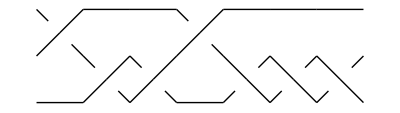

```mathematica
BraidPlot[BR[3,{-1,-2,-2,-1,2,2,2}]]
```

```mathematica
MixedSpectralAnnularKh[BR[3,{-1,-2,-2,-1,2,2,2}],0]
```

(1+1/q^2+(1/q^8+1/q^6)/t^4) Ε+(1+1/(q^4 t^2)) C[1]

```mathematica
MixedSpectralAnnularKh[BR[3,{-1,-2,-2,-1,2,2,2}],1/3]
```

(1/q^(5/3)+1/q^(1/3)+(1/q^(23/3)+1/q^(19/3))/t^4) Ε+(1/(q^(7/3) t^2)+(1/q^(11/3)+1/q^(7/3))/t) C[1]+q C[2]+C[5]/(q^(11/3) t^2)+C[6]/q^(1/3)

```mathematica
MixedSpectralAnnularKh[BR[3,{-1,-2,-2,-1,2,2,2}],2/3]
```

(1/q^(4/3)+1/q^(2/3)+(1/q^(22/3)+1/q^(20/3))/t^4) Ε+(1/(q^(8/3) t^2)+(1/q^(10/3)+1/q^(8/3))/t) C[1]+(1+1/(q^(10/3) t^2)) C[2]+C[3]/q^(2/3)

```mathematica
MixedSpectralAnnularKh[BR[3,{-1,-2,-2,-1,2,2,2}],1]
```

(2/q+2/(q^7 t^4)) Ε+(2/(q^3 t^2)+2/(q^3 t)) C[1]+(2 C[2])/q

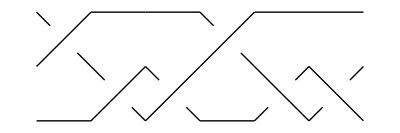

```mathematica
BraidPlot[BR[3,{-1,-2,-2,-1,2,2}]]
```

```mathematica
MixedSpectralAnnularKh[BR[3,{-1,-2,-2,-1,2,2}],0]
```

(1/q^3+3/q+2 q+(1/q^9+1/q^7)/t^4) Ε+C[1]/(q^5 t^2)

```mathematica
MixedSpectralAnnularKh[BR[3,{-1,-2,-2,-1,2,2}],1/3]
```

(1+1/q^(8/3)+2/q^(4/3)+1/q^(2/3)+q^(2/3)+(1/q^(26/3)+1/q^(22/3))/t^4) Ε+(1/(q^(10/3) t^2)+(1/q^(14/3)+1/q^(10/3))/t) C[1]+C[5]/(q^(14/3) t^2)

```mathematica
MixedSpectralAnnularKh[BR[3,{-1,-2,-2,-1,2,2}],2/3]
```

(1/q^(7/3)+2/q^(5/3)+1/q+1/q^(1/3)+q^(1/3)+(1/q^(25/3)+1/q^(23/3))/t^4) Ε+(1/(q^(11/3) t^2)+(1/q^(13/3)+1/q^(11/3))/t) C[1]+C[2]/(q^(13/3) t^2)

```mathematica
MixedSpectralAnnularKh[BR[3,{-1,-2,-2,-1,2,2}],1]
```

(2+4/q^2+2/(q^8 t^4)) Ε+(2/(q^4 t^2)+2/(q^4 t)) C[1]

```mathematica
HubbardB[0,0]=BR[4,{3, -2, -2, 3, 3, 2, -3, 1, 1, 2,-1}]
```

BR[4,{3,-2,-2,3,3,2,-3,1,1,2,-1}]

Fri 9 Dec 2016 20:23:49 computing differentials {-5,8}

Fri 9 Dec 2016 20:23:49 ... grading -5

Fri 9 Dec 2016 20:23:49 ... grading -4

Fri 9 Dec 2016 20:23:49 ... grading -3

Fri 9 Dec 2016 20:23:59 ... grading -2

Fri 9 Dec 2016 20:27:25 ... grading -1

Fri 9 Dec 2016 20:48:41 ... grading 0

Fri 9 Dec 2016 21:44:47 ... grading 1

Fri 9 Dec 2016 22:51:21 ... grading 2

Fri 9 Dec 2016 23:31:44 ... grading 3

Fri 9 Dec 2016 23:43:35 ... grading 4

Fri 9 Dec 2016 23:45:17 ... grading 5

Fri 9 Dec 2016 23:45:24 ... grading 6

Fri 9 Dec 2016 23:45:25 ... grading 7

Fri 9 Dec 2016 23:45:25 ... grading 8

Fri 9 Dec 2016 23:45:25 differentials: 2069244808 bytes

Fri 9 Dec 2016 23:45:25 computing gradings

Fri 9 Dec 2016 23:45:25 gradings: 2069244808 bytes

Fri 9 Dec 2016 23:45:26 computing gaussian elimination

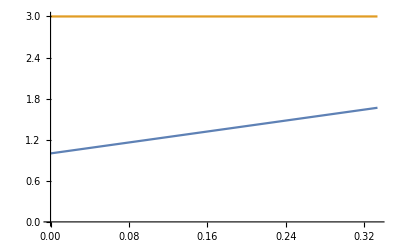

Sun 11 Dec 2016 22:36:28 computing differentials {-5,8}

Sun 11 Dec 2016 22:36:28 ... grading -5

Sun 11 Dec 2016 22:36:28 ... grading -4

Sun 11 Dec 2016 22:36:28 ... grading -3

Sun 11 Dec 2016 22:36:38 ... grading -2

Sun 11 Dec 2016 22:40:05 ... grading -1

Sun 11 Dec 2016 23:01:28 ... grading 0

Sun 11 Dec 2016 23:57:28 ... grading 1

Mon 12 Dec 2016 01:04:02 ... grading 2

Mon 12 Dec 2016 01:44:27 ... grading 3

Mon 12 Dec 2016 01:56:19 ... grading 4

Mon 12 Dec 2016 01:58:01 ... grading 5

Mon 12 Dec 2016 01:58:08 ... grading 6

Mon 12 Dec 2016 01:58:08 ... grading 7

Mon 12 Dec 2016 01:58:08 ... grading 8

Mon 12 Dec 2016 01:58:09 differentials: 2069244808 bytes

Mon 12 Dec 2016 01:58:09 computing gradings

Mon 12 Dec 2016 01:58:09 gradings: 2069244808 bytes

Mon 12 Dec 2016 01:58:09 computing gaussian elimination

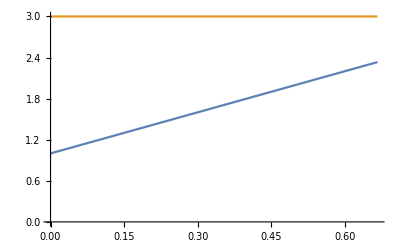

Wed 14 Dec 2016 01:32:33 computing differentials {-5,8}

Wed 14 Dec 2016 01:32:33 ... grading -5

Wed 14 Dec 2016 01:32:33 ... grading -4

Wed 14 Dec 2016 01:32:33 ... grading -3

Wed 14 Dec 2016 01:32:42 ... grading -2

Wed 14 Dec 2016 01:36:01 ... grading -1

Wed 14 Dec 2016 01:56:33 ... grading 0

Wed 14 Dec 2016 02:50:25 ... grading 1

Wed 14 Dec 2016 03:54:25 ... grading 2

Wed 14 Dec 2016 04:33:15 ... grading 3

Wed 14 Dec 2016 04:44:43 ... grading 4

Wed 14 Dec 2016 04:46:23 ... grading 5

Wed 14 Dec 2016 04:46:30 ... grading 6

Wed 14 Dec 2016 04:46:30 ... grading 7

Wed 14 Dec 2016 04:46:30 ... grading 8

Wed 14 Dec 2016 04:46:30 differentials: 2068176040 bytes

Wed 14 Dec 2016 04:46:31 computing gradings

Wed 14 Dec 2016 04:46:31 gradings: 2068176040 bytes

Wed 14 Dec 2016 04:46:31 computing gaussian elimination

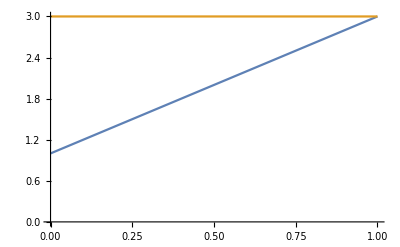

Fri 16 Dec 2016 05:03:10 computing differentials {-5,8}

Fri 16 Dec 2016 05:03:10 ... grading -5

Fri 16 Dec 2016 05:03:10 ... grading -4

Fri 16 Dec 2016 05:03:11 ... grading -3

Fri 16 Dec 2016 05:03:20 ... grading -2

Fri 16 Dec 2016 05:06:49 ... grading -1

Fri 16 Dec 2016 05:28:24 ... grading 0

Fri 16 Dec 2016 06:25:13 ... grading 1

Fri 16 Dec 2016 07:32:16 ... grading 2

Fri 16 Dec 2016 08:13:03 ... grading 3

Fri 16 Dec 2016 08:25:02 ... grading 4

Fri 16 Dec 2016 08:26:45 ... grading 5

Fri 16 Dec 2016 08:26:53 ... grading 6

Fri 16 Dec 2016 08:26:53 ... grading 7

Fri 16 Dec 2016 08:26:53 ... grading 8

Fri 16 Dec 2016 08:26:53 differentials: 2069244808 bytes

Fri 16 Dec 2016 08:26:53 computing gradings

Fri 16 Dec 2016 08:26:54 gradings: 2069244808 bytes

Fri 16 Dec 2016 08:26:54 computing gaussian elimination

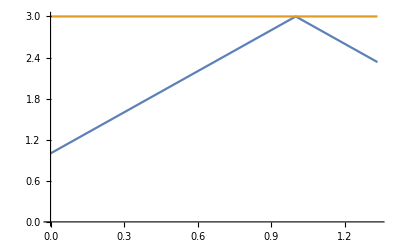

Sun 18 Dec 2016 09:15:24 computing differentials {-5,8}

Sun 18 Dec 2016 09:15:24 ... grading -5

Sun 18 Dec 2016 09:15:24 ... grading -4

Sun 18 Dec 2016 09:15:24 ... grading -3

Sun 18 Dec 2016 09:15:34 ... grading -2

Sun 18 Dec 2016 09:19:03 ... grading -1

Sun 18 Dec 2016 09:40:41 ... grading 0

Sun 18 Dec 2016 10:37:33 ... grading 1

Sun 18 Dec 2016 11:44:45 ... grading 2

Sun 18 Dec 2016 12:25:41 ... grading 3

Sun 18 Dec 2016 12:37:42 ... grading 4

Sun 18 Dec 2016 12:39:26 ... grading 5

Sun 18 Dec 2016 12:39:34 ... grading 6

Sun 18 Dec 2016 12:39:34 ... grading 7

Sun 18 Dec 2016 12:39:34 ... grading 8

Sun 18 Dec 2016 12:39:34 differentials: 2069244808 bytes

Sun 18 Dec 2016 12:39:35 computing gradings

Sun 18 Dec 2016 12:39:35 gradings: 2069244808 bytes

Sun 18 Dec 2016 12:39:35 computing gaussian elimination

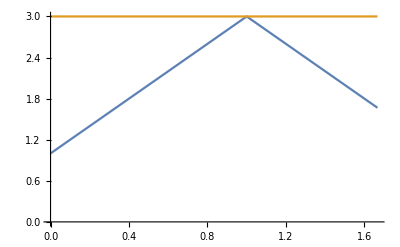

Tue 20 Dec 2016 14:41:44 computing differentials {-5,8}

Tue 20 Dec 2016 14:41:44 ... grading -5

Tue 20 Dec 2016 14:41:44 ... grading -4

Tue 20 Dec 2016 14:41:44 ... grading -3

Tue 20 Dec 2016 14:41:54 ... grading -2

Tue 20 Dec 2016 14:45:45 ... grading -1

Tue 20 Dec 2016 15:09:12 ... grading 0

Tue 20 Dec 2016 16:09:59 ... grading 1

Tue 20 Dec 2016 17:21:34 ... grading 2

Tue 20 Dec 2016 18:04:49 ... grading 3

Tue 20 Dec 2016 18:17:36 ... grading 4

Tue 20 Dec 2016 18:19:30 ... grading 5

Tue 20 Dec 2016 18:19:38 ... grading 6

Tue 20 Dec 2016 18:19:39 ... grading 7

Tue 20 Dec 2016 18:19:39 ... grading 8

Tue 20 Dec 2016 18:19:39 differentials: 2065923064 bytes

Tue 20 Dec 2016 18:19:39 computing gradings

Tue 20 Dec 2016 18:19:39 gradings: 2065923064 bytes

Tue 20 Dec 2016 18:19:40 computing gaussian elimination

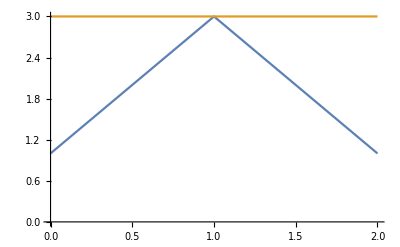

```mathematica
plotProgressive[HubbardB[0,0]]
```

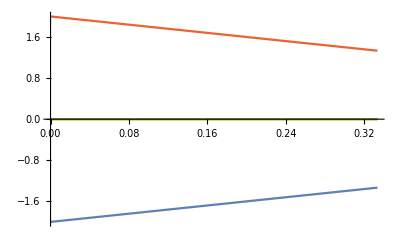

Wed 7 Dec 2016 09:23:33 computing differentials {-6,6}

Wed 7 Dec 2016 09:23:33 ... grading -6

Wed 7 Dec 2016 09:23:33 ... grading -5

Wed 7 Dec 2016 09:23:34 ... grading -4

$Aborted

```mathematica
plotProgressive[BR[4,{-3,-3, 2,-3, 2, 1, 1,-2, 1,-2}]]
```

```mathematica
Skeleton[PD[BR[3,{1,-2,1,-2,1,-2,1,-2,1,-2}]]]
```

{Loop[1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20]}

```mathematica
sInvariant[PD[BR[3,{1,-2,1,-2,1,-2,1,-2,1,-2}]]]
```

0

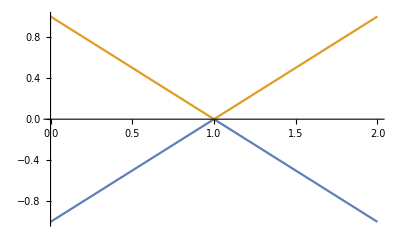

```mathematica
plotProgressive[BR[3,{1,-2,1,-2,1,-2,1,-2,1,-2}]]
```

```mathematica
MixedSInvariant[BR[4,{3,-2,-2,3,3,2,-3,-1,2,1,1}],1/3]
```

{5/3,7/3}

```mathematica
MixedSInvariant[BR[4,{3,-2,-2,3,3,2,-3,-1,2,1,1}],2/3]
```

{5/3,7/3}

```mathematica
sInvariant[PD[BR[4,{3,-2,-2,3,3,2,-3,-1,2,1,1}]]]
```

2

```mathematica
MixedSInvariant[BR[4,{3,-2,-2,3,3,2,-3,-1,2,1,1}],1/4]
```

Fri 25 Nov 2016 12:49:36 computing differentials {-5,8}

Fri 25 Nov 2016 12:49:36 ... grading -5

Fri 25 Nov 2016 12:49:36 ... grading -4

Fri 25 Nov 2016 12:49:37 ... grading -3

Fri 25 Nov 2016 12:49:47 ... grading -2

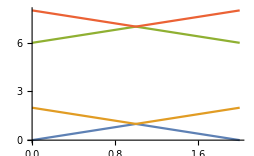

```mathematica
plotAll[BR[3,{1,2,2,1,-2,-2,-2}]]
```

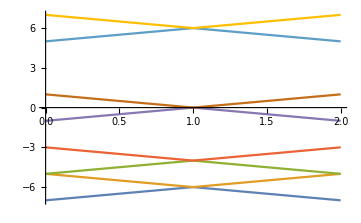

```mathematica
plotAll[BR[3,{1,2,2,1,-2,-2,-2,-2}]]
```

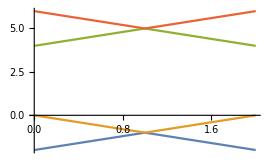

```mathematica
plotAll[BR[3,{1,2,2,1,-2,-2,-2,-2,-2}]]
```

```mathematica
sInvariant[BR[4,{2,2,1,-2,-3,-3,-2,3,2}]]
```

UniversalKh[BR[4,{2,2,1,-2,-3,-3,-2,3,2}]]

```mathematica
Kh[BR[4,{1,1,2,-1,-3,2,-3}]]
```

2/q+q+1/(q^5 t^2)+1/(q t)+q t+q^3 t+q^5 t^2+q^5 t^3+q^9 t^4

```mathematica
Kh[BR[4,{1,-2,1,-2,3,-2,3}]]
```

3/q+2 q+1/(q^7 t^3)+2/(q^5 t^2)+1/(q^3 t^2)+1/(q^3 t)+2/(q t)+2 q t+2 q^3 t+q^3 t^2+2 q^5 t^2+q^5 t^3+q^7 t^3+q^9 t^4

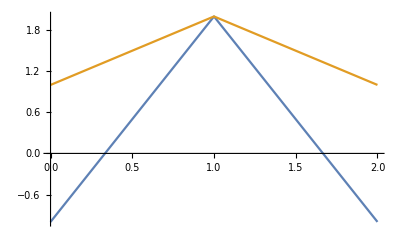

```mathematica
plotAll[BR[3,{1,1,2,2,1,-2,-2,-2}]]
```

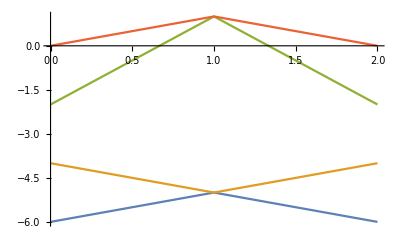

```mathematica
plotAll[BR[3,{1,1,2,2,1,-2,-2,-2,-2}]]
```

```mathematica
plotAll[BR[3,{1,1,2,2,1,-2,-2,-2,-2,-2}]]
```

Tue 15 Nov 2016 19:56:23 computing differentials {-6,6}

Tue 15 Nov 2016 19:56:23 ... grading -6

Tue 15 Nov 2016 19:56:23 ... grading -5

Tue 15 Nov 2016 19:56:28 ... grading -4

Tue 15 Nov 2016 19:59:30 ... grading -3

Tue 15 Nov 2016 20:20:40 ... grading -2

Tue 15 Nov 2016 21:14:20 ... grading -1

Tue 15 Nov 2016 22:10:29 ... grading 0

Tue 15 Nov 2016 22:37:44 ... grading 1

Tue 15 Nov 2016 22:43:34 ... grading 2

Tue 15 Nov 2016 22:44:08 ... grading 3

Tue 15 Nov 2016 22:44:10 ... grading 4

Tue 15 Nov 2016 22:44:10 ... grading 5

Tue 15 Nov 2016 22:44:10 ... grading 6

Tue 15 Nov 2016 22:44:10 differentials: 1796349752 bytes

Tue 15 Nov 2016 22:44:10 computing gradings

Tue 15 Nov 2016 22:44:10 gradings: 1796349752 bytes

Tue 15 Nov 2016 22:44:10 computing gaussian elimination

$Aborted

```mathematica
Kh[BR[4,{2,2,1,-2,-3,-3,-2,3,2}]]
```

1/q+q+1/(q^5 t^2)+1/(q t)+q t+q^5 t^2

```mathematica
Kh[BR[4,{2,2,1,-2,-3,-3,-2,3}]]
```

1+1/q^2+1/(q^6 t^2)+1/(q^4 t^2)

```mathematica
plotAll[BR[4,{2,2,1,-2,-3,-3,-2,3,2}]]
```

```mathematica
plotAll[BR[4,{2,2,1,-2,-2,-2,-2,3}]]
```

Sun 26 Jun 2016 11:53:13 computing differentials {-2,5}

Sun 26 Jun 2016 11:53:13 ... grading -2

Sun 26 Jun 2016 11:53:13 ... grading -1

Sun 26 Jun 2016 11:53:13 ... grading 0

Sun 26 Jun 2016 11:53:13 ... grading 1

Sun 26 Jun 2016 11:53:13 ... grading 2

Sun 26 Jun 2016 11:53:13 ... grading 3

Sun 26 Jun 2016 11:53:13 ... grading 4

Sun 26 Jun 2016 11:53:13 ... grading 5

Sun 26 Jun 2016 11:53:13 differentials: 130728 bytes

Sun 26 Jun 2016 11:53:13 computing gradings

Sun 26 Jun 2016 11:53:13 gradings: 130728 bytes

Sun 26 Jun 2016 11:53:13 computing gaussian elimination

Sun 26 Jun 2016 11:53:13 computing differentials {-2,5}

Sun 26 Jun 2016 11:53:13 ... grading -2

Sun 26 Jun 2016 11:53:13 ... grading -1

Sun 26 Jun 2016 11:53:13 ... grading 0

Sun 26 Jun 2016 11:53:14 ... grading 1

Sun 26 Jun 2016 11:53:14 ... grading 2

Sun 26 Jun 2016 11:53:14 ... grading 3

Sun 26 Jun 2016 11:53:14 ... grading 4

Sun 26 Jun 2016 11:53:14 ... grading 5

Sun 26 Jun 2016 11:53:14 differentials: 141256 bytes

Sun 26 Jun 2016 11:53:14 computing gradings

Sun 26 Jun 2016 11:53:14 gradings: 141256 bytes

Sun 26 Jun 2016 11:53:14 computing gaussian elimination

Sun 26 Jun 2016 11:53:14 computing differentials {-2,5}

Sun 26 Jun 2016 11:53:14 ... grading -2

Sun 26 Jun 2016 11:53:14 ... grading -1

Sun 26 Jun 2016 11:53:14 ... grading 0

Sun 26 Jun 2016 11:53:14 ... grading 1

Sun 26 Jun 2016 11:53:14 ... grading 2

Sun 26 Jun 2016 11:53:14 ... grading 3

Sun 26 Jun 2016 11:53:14 ... grading 4

Sun 26 Jun 2016 11:53:14 ... grading 5

Sun 26 Jun 2016 11:53:14 differentials: 141256 bytes

Sun 26 Jun 2016 11:53:14 computing gradings

Sun 26 Jun 2016 11:53:14 gradings: 141256 bytes

Sun 26 Jun 2016 11:53:14 computing gaussian elimination

Sun 26 Jun 2016 11:53:14 computing differentials {-2,5}

Sun 26 Jun 2016 11:53:14 ... grading -2

Sun 26 Jun 2016 11:53:14 ... grading -1

Sun 26 Jun 2016 11:53:14 ... grading 0

Sun 26 Jun 2016 11:53:15 ... grading 1

Sun 26 Jun 2016 11:53:15 ... grading 2

Sun 26 Jun 2016 11:53:15 ... grading 3

Sun 26 Jun 2016 11:53:15 ... grading 4

Sun 26 Jun 2016 11:53:15 ... grading 5

Sun 26 Jun 2016 11:53:15 differentials: 134200 bytes

Sun 26 Jun 2016 11:53:15 computing gradings

Sun 26 Jun 2016 11:53:15 gradings: 134200 bytes

Sun 26 Jun 2016 11:53:15 computing gaussian elimination

Sun 26 Jun 2016 11:53:15 computing differentials {-2,5}

Sun 26 Jun 2016 11:53:15 ... grading -2

Sun 26 Jun 2016 11:53:15 ... grading -1

Sun 26 Jun 2016 11:53:15 ... grading 0

Sun 26 Jun 2016 11:53:15 ... grading 1

Sun 26 Jun 2016 11:53:15 ... grading 2

Sun 26 Jun 2016 11:53:15 ... grading 3

Sun 26 Jun 2016 11:53:15 ... grading 4

Sun 26 Jun 2016 11:53:15 ... grading 5

Sun 26 Jun 2016 11:53:15 differentials: 141256 bytes

Sun 26 Jun 2016 11:53:15 computing gradings

Sun 26 Jun 2016 11:53:15 gradings: 141256 bytes

Sun 26 Jun 2016 11:53:15 computing gaussian elimination

Sun 26 Jun 2016 11:53:15 computing differentials {-2,5}

Sun 26 Jun 2016 11:53:15 ... grading -2

Sun 26 Jun 2016 11:53:15 ... grading -1

Sun 26 Jun 2016 11:53:15 ... grading 0

Sun 26 Jun 2016 11:53:16 ... grading 1

Sun 26 Jun 2016 11:53:16 ... grading 2

Sun 26 Jun 2016 11:53:16 ... grading 3

Sun 26 Jun 2016 11:53:16 ... grading 4

Sun 26 Jun 2016 11:53:16 ... grading 5

Sun 26 Jun 2016 11:53:16 differentials: 141256 bytes

Sun 26 Jun 2016 11:53:16 computing gradings

Sun 26 Jun 2016 11:53:16 gradings: 141256 bytes

Sun 26 Jun 2016 11:53:16 computing gaussian elimination

Sun 26 Jun 2016 11:53:16 computing differentials {-2,5}

Sun 26 Jun 2016 11:53:16 ... grading -2

Sun 26 Jun 2016 11:53:16 ... grading -1

Sun 26 Jun 2016 11:53:16 ... grading 0

Sun 26 Jun 2016 11:53:16 ... grading 1

Sun 26 Jun 2016 11:53:16 ... grading 2

Sun 26 Jun 2016 11:53:16 ... grading 3

Sun 26 Jun 2016 11:53:16 ... grading 4

Sun 26 Jun 2016 11:53:16 ... grading 5

Sun 26 Jun 2016 11:53:16 differentials: 130728 bytes

Sun 26 Jun 2016 11:53:16 computing gradings

Sun 26 Jun 2016 11:53:16 gradings: 130728 bytes

Sun 26 Jun 2016 11:53:16 computing gaussian elimination

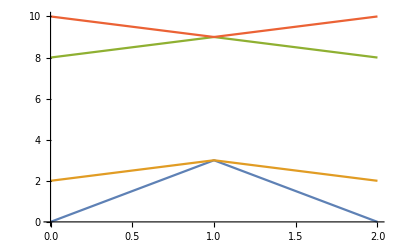

```mathematica
plotAll[BR[3,{-1,2,1,1,2}]]
```

BR[4,{1,1,2,-1,-3,2,-3}]

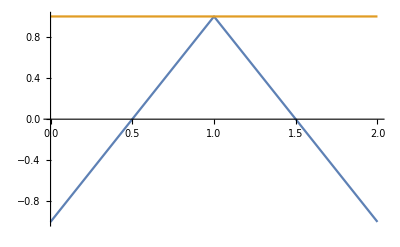

BR[4,{1,-2,1,-2,3,-2,3}]

-Graphics-

BR[5,{1,1,2,-1,2,3,-2,-4,3,-4}]

-Graphics-

BR[5,{1,1,2,-1,-3,2,-3,-4,3,-4}]

-Graphics-

BR[4,{-1,-1,-1,2,-1,2,3,-2,3}]

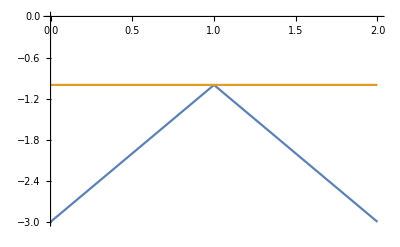

BR[4,{1,1,1,2,-1,-3,2,-3,-3}]

-Graphics-

BR[5,{1,-2,1,3,-2,-4,3,-4}]

-Graphics-

BR[4,{1,1,1,1,-2,1,3,-2,3}]

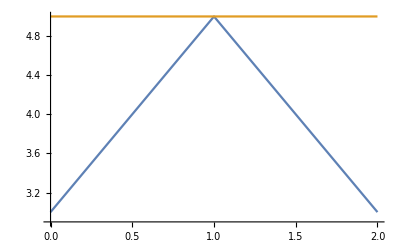

BR[5,{1,1,2,-1,-3,2,-3,4,-3,4}]

-Graphics-

BR[5,{1,1,1,2,-1,-3,2,4,-3,4}]

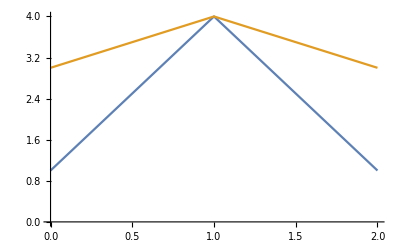

BR[5,{-1,2,-1,2,2,3,-2,-4,3,-4}]

-Graphics-

BR[5,{1,1,2,-1,2,-3,2,4,-3,4}]

-Graphics-

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
(Print[#];Print[plotAll[#]])&/@{BR[4,{1,1,2,-1,-3,2,-3}],BR[4,{1,-2,1,-2,3,-2,3}],BR[5,{1,1,2,-1,2,3,-2,-4,3,-4}],BR[5,{1,1,2,-1,-3,2,-3,-4,3,-4}],BR[4,{-1,-1,-1,2,-1,2,3,-2,3}],BR[4,{1,1,1,2,-1,-3,2,-3,-3}],BR[5,{1,-2,1,3,-2,-4,3,-4}],BR[4,{-1,-1,2,-1,2,2,3,-2,3}],BR[4,{1,1,1,1,-2,1,3,-2,3}],BR[5,{1,1,2,-1,-3,2,-3,4,-3,4}],BR[5,{1,1,1,2,-1,-3,2,4,-3,4}],BR[5,{-1,2,-1,2,2,3,-2,-4,3,-4}],BR[5,{1,1,2,-1,2,-3,2,4,-3,4}]}
```

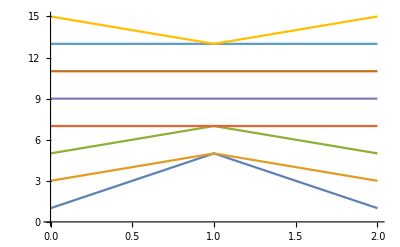

```mathematica
plotAll[BR[4,{-1,3,2,1,1,2,3}]]
```

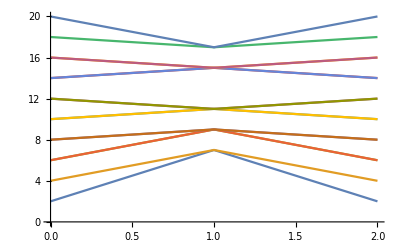

```mathematica
plotAll[BR[5,{-1,4,3,2,1,1,2,3,4}]]
```

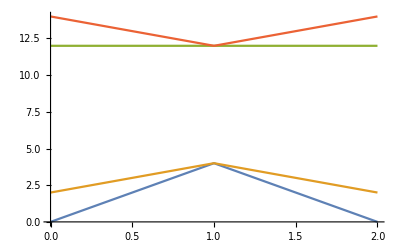

```mathematica
plotAll[BR[4,{-1,-2,3,2,1,1,2,3}]]
```

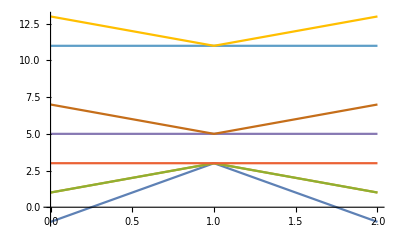

```mathematica
plotAll[BR[4,{-1,-2,-1,3,2,1,1,2,3}]]
```

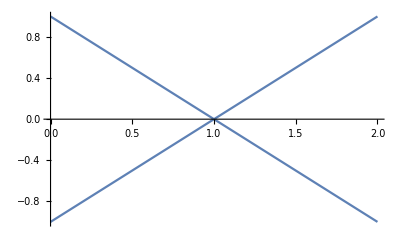

```mathematica
plot[BR[9,{1,-2,3,-4,5,-6,7,-8}]]
```

```mathematica
plot[BR[9,{1,2,-3,-4,5,-6,7,-8}]]
```

-Graphics-

```mathematica
plot[BR[9,{1,-2,-3,4,5,6,-7,-8}]]
```

-Graphics-

```mathematica
plot[BR[9,{-1,2,-3,-4,5,6,7,-8}]]
```

Mon 4 Apr 2016 08:05:41 computing differentials {-5,5}

Mon 4 Apr 2016 08:05:53 ... grading -5

Mon 4 Apr 2016 08:05:53 ... grading -4

Mon 4 Apr 2016 08:05:55 ... grading -3

Mon 4 Apr 2016 08:07:03 ... grading -2

Mon 4 Apr 2016 08:16:21 ... grading -1

Mon 4 Apr 2016 08:38:41 ... grading 0

Mon 4 Apr 2016 08:56:47 ... grading 1

Mon 4 Apr 2016 09:01:41 ... grading 2

Mon 4 Apr 2016 09:02:05 ... grading 3

Mon 4 Apr 2016 09:02:05 ... grading 4

Mon 4 Apr 2016 09:02:05 ... grading 5

Mon 4 Apr 2016 09:02:05 differentials: 769005136 bytes

Mon 4 Apr 2016 09:02:06 computing gradings

Mon 4 Apr 2016 09:02:06 gradings: 769005136 bytes

Mon 4 Apr 2016 09:02:06 computing gaussian elimination

$Aborted

```mathematica
plot[BR[9,{-1,-2,3,-4,5,6,-7,-8}]]
```

```mathematica
MixedSpectralAnnularKh[BR[Knot[3,1]],2]
```

Tue 23 Feb 2016 09:23:30 computing differentials {-4,1}

Tue 23 Feb 2016 09:23:30 ... grading -4

Tue 23 Feb 2016 09:23:30 ... grading -3

Tue 23 Feb 2016 09:23:30 ... grading -2

Tue 23 Feb 2016 09:23:30 ... grading -1

Tue 23 Feb 2016 09:23:30 ... grading 0

Tue 23 Feb 2016 09:23:30 ... grading 1

Tue 23 Feb 2016 09:23:30 differentials: 6984 bytes

Tue 23 Feb 2016 09:23:30 computing gradings

Tue 23 Feb 2016 09:23:30 gradings: 6984 bytes

Tue 23 Feb 2016 09:23:30 computing gaussian elimination

(1/q^3+1/q) Ε+C[1]/(q^9 t^3)

```mathematica
MixedSpectralAnnularKh[BR[Knot[3,1]],3/2]
```

Fri 11 Dec 2015 10:36:39 computing differentials {-4,1}

Fri 11 Dec 2015 10:36:39 ... grading -4

Fri 11 Dec 2015 10:36:39 ... grading -3

Fri 11 Dec 2015 10:36:39 ... grading -2

Fri 11 Dec 2015 10:36:39 ... grading -1

Fri 11 Dec 2015 10:36:39 ... grading 0

Fri 11 Dec 2015 10:36:39 ... grading 1

Fri 11 Dec 2015 10:36:39 differentials: 8016 bytes

Fri 11 Dec 2015 10:36:39 computing gradings

Fri 11 Dec 2015 10:36:39 gradings: 8016 bytes

Fri 11 Dec 2015 10:36:39 computing gaussian elimination

(1/q^3+1/q^2) Ε+C[1]/(q^5 t)+C[4]/(q^9 t^3)

```mathematica
MixedSpectralAnnularKh[BR[Knot[3,1]],1]
```

Fri 11 Dec 2015 10:36:39 computing differentials {-4,1}

Fri 11 Dec 2015 10:36:39 ... grading -4

Fri 11 Dec 2015 10:36:39 ... grading -3

Fri 11 Dec 2015 10:36:39 ... grading -2

Fri 11 Dec 2015 10:36:39 ... grading -1

Fri 11 Dec 2015 10:36:39 ... grading 0

Fri 11 Dec 2015 10:36:39 ... grading 1

Fri 11 Dec 2015 10:36:39 differentials: 7800 bytes

Fri 11 Dec 2015 10:36:39 computing gradings

Fri 11 Dec 2015 10:36:39 gradings: 7800 bytes

Fri 11 Dec 2015 10:36:39 computing gaussian elimination

(2 Ε)/q^3+C[1]/(q^5 t)+C[2]/(q^9 t^3)

```mathematica
MixedSpectralAnnularKh[BR[Knot[3,1]],2/3]
```

Fri 11 Dec 2015 10:36:39 computing differentials {-4,1}

Fri 11 Dec 2015 10:36:39 ... grading -4

Fri 11 Dec 2015 10:36:39 ... grading -3

Fri 11 Dec 2015 10:36:39 ... grading -2

Fri 11 Dec 2015 10:36:39 ... grading -1

Fri 11 Dec 2015 10:36:39 ... grading 0

Fri 11 Dec 2015 10:36:39 ... grading 1

Fri 11 Dec 2015 10:36:39 differentials: 8016 bytes

Fri 11 Dec 2015 10:36:39 computing gradings

Fri 11 Dec 2015 10:36:39 gradings: 8016 bytes

Fri 11 Dec 2015 10:36:39 computing gaussian elimination

(1/q^3+1/q^(7/3)) Ε+C[1]/(q^5 t)+C[3]/(q^9 t^3)

```mathematica
MixedSpectralAnnularKh[BR[Knot[3,1]],1/2]
```

Fri 11 Dec 2015 10:36:40 computing differentials {-4,1}

Fri 11 Dec 2015 10:36:40 ... grading -4

Fri 11 Dec 2015 10:36:40 ... grading -3

Fri 11 Dec 2015 10:36:40 ... grading -2

Fri 11 Dec 2015 10:36:40 ... grading -1

Fri 11 Dec 2015 10:36:40 ... grading 0

Fri 11 Dec 2015 10:36:40 ... grading 1

Fri 11 Dec 2015 10:36:40 differentials: 8016 bytes

Fri 11 Dec 2015 10:36:40 computing gradings

Fri 11 Dec 2015 10:36:40 gradings: 8016 bytes

Fri 11 Dec 2015 10:36:40 computing gaussian elimination

(1/q^3+1/q^2) Ε+C[1]/(q^5 t)+C[4]/(q^9 t^3)

```mathematica
MixedSpectralAnnularKh[BR[Knot[3,1]],0]
```

Fri 11 Dec 2015 10:36:40 computing differentials {-4,1}

Fri 11 Dec 2015 10:36:40 ... grading -4

Fri 11 Dec 2015 10:36:40 ... grading -3

Fri 11 Dec 2015 10:36:40 ... grading -2

Fri 11 Dec 2015 10:36:40 ... grading -1

Fri 11 Dec 2015 10:36:40 ... grading 0

Fri 11 Dec 2015 10:36:40 ... grading 1

Fri 11 Dec 2015 10:36:40 differentials: 6984 bytes

Fri 11 Dec 2015 10:36:40 computing gradings

Fri 11 Dec 2015 10:36:40 gradings: 6984 bytes

Fri 11 Dec 2015 10:36:40 computing gaussian elimination

(1/q^3+1/q) Ε+C[1]/(q^9 t^3)

```mathematica
Do[Print[{r,MixedSInvariant[BR[Knot[9,42]],r]}],{r,1/3,2,1/3}]
```

Wed 24 Feb 2016 11:48:15 computing differentials {-5,6}

Wed 24 Feb 2016 11:48:24 ... grading -5

Wed 24 Feb 2016 11:48:24 ... grading -4

Wed 24 Feb 2016 11:48:24 ... grading -3

Wed 24 Feb 2016 11:48:28 ... grading -2

Wed 24 Feb 2016 11:49:09 ... grading -1

Wed 24 Feb 2016 11:52:19 ... grading 0

Wed 24 Feb 2016 11:58:30 ... grading 1

Wed 24 Feb 2016 12:03:45 ... grading 2

Wed 24 Feb 2016 12:05:33 ... grading 3

Wed 24 Feb 2016 12:05:47 ... grading 4

Wed 24 Feb 2016 12:05:47 ... grading 5

Wed 24 Feb 2016 12:05:47 ... grading 6

Wed 24 Feb 2016 12:05:47 differentials: 192152216 bytes

Wed 24 Feb 2016 12:05:47 computing gradings

Wed 24 Feb 2016 12:05:48 gradings: 192152216 bytes

Wed 24 Feb 2016 12:05:48 computing gaussian elimination

{1/3,{-1/3,1}}

Wed 24 Feb 2016 13:32:21 computing differentials {-5,6}

Wed 24 Feb 2016 13:32:21 ... grading -5

Wed 24 Feb 2016 13:32:21 ... grading -4

Wed 24 Feb 2016 13:32:22 ... grading -3

Wed 24 Feb 2016 13:32:25 ... grading -2

Wed 24 Feb 2016 13:33:04 ... grading -1

Wed 24 Feb 2016 13:36:11 ... grading 0

Wed 24 Feb 2016 13:42:13 ... grading 1

Wed 24 Feb 2016 13:47:16 ... grading 2

Wed 24 Feb 2016 13:48:58 ... grading 3

Wed 24 Feb 2016 13:49:10 ... grading 4

Wed 24 Feb 2016 13:49:10 ... grading 5

Wed 24 Feb 2016 13:49:10 ... grading 6

Wed 24 Feb 2016 13:49:10 differentials: 192152216 bytes

Wed 24 Feb 2016 13:49:10 computing gradings

Wed 24 Feb 2016 13:49:10 gradings: 192152216 bytes

Wed 24 Feb 2016 13:49:10 computing gaussian elimination

{2/3,{1/3,1}}

Wed 24 Feb 2016 15:15:34 computing differentials {-5,6}

Wed 24 Feb 2016 15:15:34 ... grading -5

Wed 24 Feb 2016 15:15:34 ... grading -4

Wed 24 Feb 2016 15:15:34 ... grading -3

Wed 24 Feb 2016 15:15:38 ... grading -2

Wed 24 Feb 2016 15:16:15 ... grading -1

Wed 24 Feb 2016 15:19:12 ... grading 0

Wed 24 Feb 2016 15:24:57 ... grading 1

Wed 24 Feb 2016 15:29:45 ... grading 2

Wed 24 Feb 2016 15:31:22 ... grading 3

Wed 24 Feb 2016 15:31:34 ... grading 4

Wed 24 Feb 2016 15:31:34 ... grading 5

Wed 24 Feb 2016 15:31:34 ... grading 6

Wed 24 Feb 2016 15:31:34 differentials: 191938376 bytes

Wed 24 Feb 2016 15:31:35 computing gradings

Wed 24 Feb 2016 15:31:35 gradings: 191938376 bytes

Wed 24 Feb 2016 15:31:35 computing gaussian elimination

{1,{1}}

Wed 24 Feb 2016 16:56:59 computing differentials {-5,6}

Wed 24 Feb 2016 16:56:59 ... grading -5

Wed 24 Feb 2016 16:56:59 ... grading -4

Wed 24 Feb 2016 16:57:00 ... grading -3

Wed 24 Feb 2016 16:57:03 ... grading -2

Wed 24 Feb 2016 16:57:42 ... grading -1

Wed 24 Feb 2016 17:00:45 ... grading 0

Wed 24 Feb 2016 17:06:41 ... grading 1

Wed 24 Feb 2016 17:11:41 ... grading 2

Wed 24 Feb 2016 17:13:22 ... grading 3

Wed 24 Feb 2016 17:13:34 ... grading 4

Wed 24 Feb 2016 17:13:34 ... grading 5

Wed 24 Feb 2016 17:13:34 ... grading 6

Wed 24 Feb 2016 17:13:34 differentials: 192152216 bytes

Wed 24 Feb 2016 17:13:35 computing gradings

Wed 24 Feb 2016 17:13:35 gradings: 192152216 bytes

Wed 24 Feb 2016 17:13:35 computing gaussian elimination

{4/3,{1/3,1}}

Wed 24 Feb 2016 18:38:57 computing differentials {-5,6}

Wed 24 Feb 2016 18:38:57 ... grading -5

Wed 24 Feb 2016 18:38:57 ... grading -4

Wed 24 Feb 2016 18:38:57 ... grading -3

Wed 24 Feb 2016 18:39:00 ... grading -2

Wed 24 Feb 2016 18:39:39 ... grading -1

Wed 24 Feb 2016 18:42:42 ... grading 0

Wed 24 Feb 2016 18:48:37 ... grading 1

Wed 24 Feb 2016 18:53:38 ... grading 2

Wed 24 Feb 2016 18:55:18 ... grading 3

Wed 24 Feb 2016 18:55:31 ... grading 4

Wed 24 Feb 2016 18:55:31 ... grading 5

Wed 24 Feb 2016 18:55:31 ... grading 6

Wed 24 Feb 2016 18:55:31 differentials: 192152216 bytes

Wed 24 Feb 2016 18:55:31 computing gradings

Wed 24 Feb 2016 18:55:31 gradings: 192152216 bytes

Wed 24 Feb 2016 18:55:31 computing gaussian elimination

{5/3,{-1/3,1}}

Wed 24 Feb 2016 20:21:01 computing differentials {-5,6}

Wed 24 Feb 2016 20:21:01 ... grading -5

Wed 24 Feb 2016 20:21:01 ... grading -4

Wed 24 Feb 2016 20:21:01 ... grading -3

Wed 24 Feb 2016 20:21:04 ... grading -2

Wed 24 Feb 2016 20:21:40 ... grading -1

Wed 24 Feb 2016 20:24:30 ... grading 0

Wed 24 Feb 2016 20:30:04 ... grading 1

Wed 24 Feb 2016 20:34:44 ... grading 2

Wed 24 Feb 2016 20:36:17 ... grading 3

Wed 24 Feb 2016 20:36:28 ... grading 4

Wed 24 Feb 2016 20:36:29 ... grading 5

Wed 24 Feb 2016 20:36:29 ... grading 6

Wed 24 Feb 2016 20:36:29 differentials: 191363528 bytes

Wed 24 Feb 2016 20:36:29 computing gradings

Wed 24 Feb 2016 20:36:29 gradings: 191363528 bytes

Wed 24 Feb 2016 20:36:29 computing gaussian elimination

{2,{-1,1}}

```mathematica
Do[Print[{r,MixedSInvariant[(* 10_136, from Vaughan's Hecke algebras paper *)BR[4,{1,1,2,-3,2,-1,2,2,-3,-2,-2}],r]}],{r,1/3,2,1/3}]
```

Wed 24 Feb 2016 22:01:17 computing differentials {-6,7}

Wed 24 Feb 2016 22:02:01 ... grading -6

Wed 24 Feb 2016 22:02:01 ... grading -5

Wed 24 Feb 2016 22:02:02 ... grading -4

Wed 24 Feb 2016 22:02:13 ... grading -3

Wed 24 Feb 2016 22:04:30 ... grading -2

Wed 24 Feb 2016 22:21:59 ... grading -1

Wed 24 Feb 2016 23:29:50 ... grading 0

Thu 25 Feb 2016 01:43:09 ... grading 1

Thu 25 Feb 2016 03:53:57 ... grading 2

Thu 25 Feb 2016 05:01:11 ... grading 3

Thu 25 Feb 2016 05:17:00 ... grading 4

Thu 25 Feb 2016 05:18:31 ... grading 5

Thu 25 Feb 2016 05:18:34 ... grading 6

Thu 25 Feb 2016 05:18:34 ... grading 7

Thu 25 Feb 2016 05:18:34 differentials: 4050463200 bytes

Thu 25 Feb 2016 05:18:35 computing gradings

Thu 25 Feb 2016 05:18:35 gradings: 4050463200 bytes

Thu 25 Feb 2016 05:18:36 computing gaussian elimination

{1/3,{-1/3,1}}

Wed 2 Mar 2016 04:52:40 computing differentials {-6,7}

Wed 2 Mar 2016 04:52:40 ... grading -6

Wed 2 Mar 2016 04:52:40 ... grading -5

Wed 2 Mar 2016 04:52:41 ... grading -4

Wed 2 Mar 2016 04:52:49 ... grading -3

Wed 2 Mar 2016 04:54:58 ... grading -2

Wed 2 Mar 2016 05:12:22 ... grading -1

Wed 2 Mar 2016 06:19:32 ... grading 0

Wed 2 Mar 2016 08:31:32 ... grading 1

Wed 2 Mar 2016 10:45:39 ... grading 2

Wed 2 Mar 2016 11:55:03 ... grading 3

Wed 2 Mar 2016 12:10:54 ... grading 4

Wed 2 Mar 2016 12:12:16 ... grading 5

Wed 2 Mar 2016 12:12:18 ... grading 6

Wed 2 Mar 2016 12:12:18 ... grading 7

Wed 2 Mar 2016 12:12:18 differentials: 4050463200 bytes

Wed 2 Mar 2016 12:12:19 computing gradings

Wed 2 Mar 2016 12:12:19 gradings: 4050463200 bytes

Wed 2 Mar 2016 12:12:20 computing gaussian elimination

{2/3,{1/3,1}}

Tue 8 Mar 2016 16:21:23 computing differentials {-6,7}

Tue 8 Mar 2016 16:21:23 ... grading -6

Tue 8 Mar 2016 16:21:23 ... grading -5

Tue 8 Mar 2016 16:21:24 ... grading -4

Tue 8 Mar 2016 16:21:32 ... grading -3

Tue 8 Mar 2016 16:23:42 ... grading -2

Tue 8 Mar 2016 16:41:00 ... grading -1

Tue 8 Mar 2016 17:48:27 ... grading 0

Tue 8 Mar 2016 19:51:28 ... grading 1

Tue 8 Mar 2016 21:52:32 ... grading 2

Tue 8 Mar 2016 22:54:01 ... grading 3

Tue 8 Mar 2016 23:08:04 ... grading 4

Tue 8 Mar 2016 23:09:17 ... grading 5

Tue 8 Mar 2016 23:09:19 ... grading 6

Tue 8 Mar 2016 23:09:19 ... grading 7

Tue 8 Mar 2016 23:09:19 differentials: 4047486144 bytes

Tue 8 Mar 2016 23:09:19 computing gradings

Tue 8 Mar 2016 23:09:20 gradings: 4047486144 bytes

Tue 8 Mar 2016 23:09:20 computing gaussian elimination

$Aborted

```mathematica
Do[Print[{r,MixedSInvariant[BR[Knot[10,136]],r]}],{r,1/3,2,1/3}]
```

Tue 23 Feb 2016 09:23:47 computing differentials {-5,7}

Tue 23 Feb 2016 09:24:16 ... grading -5

Tue 23 Feb 2016 09:24:16 ... grading -4

Tue 23 Feb 2016 09:24:17 ... grading -3

Tue 23 Feb 2016 09:24:33 ... grading -2

Tue 23 Feb 2016 09:26:41 ... grading -1

Tue 23 Feb 2016 09:35:55 ... grading 0

Tue 23 Feb 2016 09:54:20 ... grading 1

Tue 23 Feb 2016 10:11:57 ... grading 2

Tue 23 Feb 2016 10:20:04 ... grading 3

Tue 23 Feb 2016 10:22:00 ... grading 4

Tue 23 Feb 2016 10:22:13 ... grading 5

Tue 23 Feb 2016 10:22:13 ... grading 6

Tue 23 Feb 2016 10:22:13 ... grading 7

Tue 23 Feb 2016 10:22:13 differentials: 563386512 bytes

Tue 23 Feb 2016 10:22:14 computing gradings

Tue 23 Feb 2016 10:22:14 gradings: 563386512 bytes

Tue 23 Feb 2016 10:22:14 computing gaussian elimination

{1/3,{0,4/3}}

Tue 23 Feb 2016 16:37:32 computing differentials {-5,7}

Tue 23 Feb 2016 16:37:32 ... grading -5

Tue 23 Feb 2016 16:37:32 ... grading -4

Tue 23 Feb 2016 16:37:33 ... grading -3

Tue 23 Feb 2016 16:37:47 ... grading -2

Tue 23 Feb 2016 16:39:47 ... grading -1

Tue 23 Feb 2016 16:48:01 ... grading 0

Tue 23 Feb 2016 17:03:49 ... grading 1

Tue 23 Feb 2016 17:19:14 ... grading 2

Tue 23 Feb 2016 17:26:09 ... grading 3

Tue 23 Feb 2016 17:27:41 ... grading 4

Tue 23 Feb 2016 17:27:50 ... grading 5

Tue 23 Feb 2016 17:27:51 ... grading 6

Tue 23 Feb 2016 17:27:51 ... grading 7

Tue 23 Feb 2016 17:27:51 differentials: 563386512 bytes

Tue 23 Feb 2016 17:27:51 computing gradings

Tue 23 Feb 2016 17:27:51 gradings: 563386512 bytes

Tue 23 Feb 2016 17:27:51 computing gaussian elimination

{2/3,{1,5/3}}

Tue 23 Feb 2016 23:51:44 computing differentials {-5,7}

Tue 23 Feb 2016 23:51:44 ... grading -5

Tue 23 Feb 2016 23:51:44 ... grading -4

Tue 23 Feb 2016 23:51:45 ... grading -3

Tue 23 Feb 2016 23:51:59 ... grading -2

Tue 23 Feb 2016 23:53:59 ... grading -1

Wed 24 Feb 2016 00:02:20 ... grading 0

Wed 24 Feb 2016 00:18:20 ... grading 1

Wed 24 Feb 2016 00:33:33 ... grading 2

Wed 24 Feb 2016 00:40:30 ... grading 3

Wed 24 Feb 2016 00:42:02 ... grading 4

Wed 24 Feb 2016 00:42:11 ... grading 5

Wed 24 Feb 2016 00:42:11 ... grading 6

Wed 24 Feb 2016 00:42:11 ... grading 7

Wed 24 Feb 2016 00:42:11 differentials: 562466064 bytes

Wed 24 Feb 2016 00:42:12 computing gradings

Wed 24 Feb 2016 00:42:12 gradings: 562466064 bytes

Wed 24 Feb 2016 00:42:12 computing gaussian elimination

{1,{2}}

Wed 24 Feb 2016 07:08:59 computing differentials {-5,7}

Wed 24 Feb 2016 07:08:59 ... grading -5

Wed 24 Feb 2016 07:08:59 ... grading -4

Wed 24 Feb 2016 07:09:00 ... grading -3

Wed 24 Feb 2016 07:09:15 ... grading -2

Wed 24 Feb 2016 07:11:22 ... grading -1

Wed 24 Feb 2016 07:20:07 ... grading 0

Wed 24 Feb 2016 07:36:51 ... grading 1

Wed 24 Feb 2016 07:52:48 ... grading 2

Wed 24 Feb 2016 08:00:03 ... grading 3

Wed 24 Feb 2016 08:01:41 ... grading 4

Wed 24 Feb 2016 08:01:51 ... grading 5

Wed 24 Feb 2016 08:01:51 ... grading 6

Wed 24 Feb 2016 08:01:51 ... grading 7

Wed 24 Feb 2016 08:01:51 differentials: 563386512 bytes

Wed 24 Feb 2016 08:01:51 computing gradings

Wed 24 Feb 2016 08:01:51 gradings: 563386512 bytes

Wed 24 Feb 2016 08:01:51 computing gaussian elimination

$Aborted

```mathematica
Table[MixedSInvariant[BR[Knot[3,1]],r],{r,0,2,1/3}]
```

Null

Null

Null

«74 more identical outputs»

Null

```mathematica
Do[Print[{r,MixedSInvariant[BR[4,{-3,2,3,1,3,-2,1,1,2}],r]}],{r,1/3,2,1/3}]
```

Null

Null

Null

«105 more identical outputs»

```mathematica
Do[Print[{r,MixedSInvariant[BR[4,{3,2,1,-3,-2,1,1,2,3}],r]}],{r,1/3,2,1/3}]
```

Wed 2 Dec 2015 18:57:07 computing differentials {-3,8}

Wed 2 Dec 2015 18:57:15 ... grading -3

Wed 2 Dec 2015 18:57:15 ... grading -2

Wed 2 Dec 2015 18:57:15 ... grading -1

Wed 2 Dec 2015 18:57:21 ... grading 0

Wed 2 Dec 2015 18:58:08 ... grading 1

Wed 2 Dec 2015 19:00:50 ... grading 2

Wed 2 Dec 2015 19:04:51 ... grading 3

Wed 2 Dec 2015 19:07:41 ... grading 4

Wed 2 Dec 2015 19:08:39 ... grading 5

Wed 2 Dec 2015 19:08:48 ... grading 6

Wed 2 Dec 2015 19:08:49 ... grading 7

Wed 2 Dec 2015 19:08:49 ... grading 8

Wed 2 Dec 2015 19:08:49 differentials: 75428040 bytes

Wed 2 Dec 2015 19:08:49 computing gradings

Wed 2 Dec 2015 19:08:49 gradings: 75428040 bytes

Wed 2 Dec 2015 19:08:49 computing gaussian elimination

{1/3,{7/3,11/3}}

Wed 2 Dec 2015 19:42:54 computing differentials {-3,8}

Wed 2 Dec 2015 19:42:54 ... grading -3

Wed 2 Dec 2015 19:42:54 ... grading -2

Wed 2 Dec 2015 19:42:54 ... grading -1

Wed 2 Dec 2015 19:42:59 ... grading 0

Wed 2 Dec 2015 19:43:46 ... grading 1

Wed 2 Dec 2015 19:46:32 ... grading 2

Wed 2 Dec 2015 19:50:45 ... grading 3

Wed 2 Dec 2015 19:53:26 ... grading 4

Wed 2 Dec 2015 19:54:17 ... grading 5

Wed 2 Dec 2015 19:54:23 ... grading 6

Wed 2 Dec 2015 19:54:24 ... grading 7

Wed 2 Dec 2015 19:54:24 ... grading 8

Wed 2 Dec 2015 19:54:24 differentials: 75428040 bytes

Wed 2 Dec 2015 19:54:24 computing gradings

Wed 2 Dec 2015 19:54:24 gradings: 75428040 bytes

Wed 2 Dec 2015 19:54:24 computing gaussian elimination

{2/3,{11/3,13/3}}

Wed 2 Dec 2015 20:24:23 computing differentials {-3,8}

Wed 2 Dec 2015 20:24:23 ... grading -3

Wed 2 Dec 2015 20:24:23 ... grading -2

Wed 2 Dec 2015 20:24:23 ... grading -1

Wed 2 Dec 2015 20:24:27 ... grading 0

Wed 2 Dec 2015 20:25:05 ... grading 1

Wed 2 Dec 2015 20:27:16 ... grading 2

Wed 2 Dec 2015 20:30:34 ... grading 3

Wed 2 Dec 2015 20:32:53 ... grading 4

Wed 2 Dec 2015 20:33:36 ... grading 5

Wed 2 Dec 2015 20:33:42 ... grading 6

Wed 2 Dec 2015 20:33:42 ... grading 7

Wed 2 Dec 2015 20:33:42 ... grading 8

Wed 2 Dec 2015 20:33:42 differentials: 75197784 bytes

Wed 2 Dec 2015 20:33:42 computing gradings

Wed 2 Dec 2015 20:33:42 gradings: 75197784 bytes

Wed 2 Dec 2015 20:33:42 computing gaussian elimination

{1,{5}}

Wed 2 Dec 2015 21:05:59 computing differentials {-3,8}

Wed 2 Dec 2015 21:05:59 ... grading -3

Wed 2 Dec 2015 21:05:59 ... grading -2

Wed 2 Dec 2015 21:05:59 ... grading -1

Wed 2 Dec 2015 21:06:04 ... grading 0

Wed 2 Dec 2015 21:06:56 ... grading 1

Wed 2 Dec 2015 21:09:57 ... grading 2

Wed 2 Dec 2015 21:14:23 ... grading 3

Wed 2 Dec 2015 21:17:37 ... grading 4

Wed 2 Dec 2015 21:18:38 ... grading 5

Wed 2 Dec 2015 21:18:46 ... grading 6

Wed 2 Dec 2015 21:18:47 ... grading 7

Wed 2 Dec 2015 21:18:47 ... grading 8

Wed 2 Dec 2015 21:18:47 differentials: 75428040 bytes

Wed 2 Dec 2015 21:18:47 computing gradings

Wed 2 Dec 2015 21:18:47 gradings: 75428040 bytes

Wed 2 Dec 2015 21:18:47 computing gaussian elimination

{4/3,{11/3,13/3}}

Wed 2 Dec 2015 21:55:52 computing differentials {-3,8}

Wed 2 Dec 2015 21:55:52 ... grading -3

Wed 2 Dec 2015 21:55:52 ... grading -2

Wed 2 Dec 2015 21:55:52 ... grading -1

Wed 2 Dec 2015 21:55:57 ... grading 0

Wed 2 Dec 2015 21:56:42 ... grading 1

Wed 2 Dec 2015 21:59:22 ... grading 2

Wed 2 Dec 2015 22:03:19 ... grading 3

Wed 2 Dec 2015 22:06:14 ... grading 4

Wed 2 Dec 2015 22:07:06 ... grading 5

Wed 2 Dec 2015 22:07:14 ... grading 6

Wed 2 Dec 2015 22:07:14 ... grading 7

Wed 2 Dec 2015 22:07:14 ... grading 8

Wed 2 Dec 2015 22:07:14 differentials: 75428040 bytes

Wed 2 Dec 2015 22:07:14 computing gradings

Wed 2 Dec 2015 22:07:14 gradings: 75428040 bytes

Wed 2 Dec 2015 22:07:14 computing gaussian elimination

{5/3,{7/3,11/3}}

Wed 2 Dec 2015 22:42:35 computing differentials {-3,8}

Wed 2 Dec 2015 22:42:35 ... grading -3

Wed 2 Dec 2015 22:42:35 ... grading -2

Wed 2 Dec 2015 22:42:35 ... grading -1

Wed 2 Dec 2015 22:42:40 ... grading 0

Wed 2 Dec 2015 22:43:26 ... grading 1

Wed 2 Dec 2015 22:46:04 ... grading 2

Wed 2 Dec 2015 22:50:03 ... grading 3

Wed 2 Dec 2015 22:52:41 ... grading 4

Wed 2 Dec 2015 22:53:29 ... grading 5

Wed 2 Dec 2015 22:53:36 ... grading 6

Wed 2 Dec 2015 22:53:36 ... grading 7

Wed 2 Dec 2015 22:53:36 ... grading 8

Wed 2 Dec 2015 22:53:36 differentials: 74904144 bytes

Wed 2 Dec 2015 22:53:36 computing gradings

Wed 2 Dec 2015 22:53:36 gradings: 74904144 bytes

Wed 2 Dec 2015 22:53:36 computing gaussian elimination

{2,{1,3}}

```mathematica
Do[Print[{r,MixedSInvariant[BR[3,{-1,-1,-1,-1,-1,2,1,1,1,2}],r]}],{r,1/3,2,1/3}]
```

Mon 30 Nov 2015 16:57:30 computing differentials {-6,6}

Mon 30 Nov 2015 16:57:55 ... grading -6

Mon 30 Nov 2015 16:57:55 ... grading -5

Mon 30 Nov 2015 16:58:14 ... grading -4

Mon 30 Nov 2015 17:10:25 ... grading -3

Mon 30 Nov 2015 18:35:09 ... grading -2

Mon 30 Nov 2015 22:19:53 ... grading -1

Tue 1 Dec 2015 02:19:09 ... grading 0

Tue 1 Dec 2015 04:07:47 ... grading 1

Tue 1 Dec 2015 04:29:10 ... grading 2

Tue 1 Dec 2015 04:30:57 ... grading 3

Tue 1 Dec 2015 04:31:03 ... grading 4

Tue 1 Dec 2015 04:31:04 ... grading 5

Tue 1 Dec 2015 04:31:04 ... grading 6

Tue 1 Dec 2015 04:31:04 differentials: 3661409592 bytes

Tue 1 Dec 2015 04:31:05 computing gradings

Tue 1 Dec 2015 04:31:05 gradings: 3661409592 bytes

Tue 1 Dec 2015 04:31:06 computing gaussian elimination

{1/3,{-2,-2/3}}

Thu 10 Dec 2015 20:17:30 computing differentials {-6,6}

Thu 10 Dec 2015 20:17:30 ... grading -6

Thu 10 Dec 2015 20:17:30 ... grading -5

Thu 10 Dec 2015 20:17:46 ... grading -4

Thu 10 Dec 2015 20:27:58 ... grading -3

Thu 10 Dec 2015 21:53:08 ... grading -2

Fri 11 Dec 2015 01:39:12 ... grading -1

Fri 11 Dec 2015 05:42:19 ... grading 0

Fri 11 Dec 2015 07:30:37 ... grading 1

Fri 11 Dec 2015 07:51:50 ... grading 2

Fri 11 Dec 2015 07:53:31 ... grading 3

Fri 11 Dec 2015 07:53:35 ... grading 4

Fri 11 Dec 2015 07:53:35 ... grading 5

Fri 11 Dec 2015 07:53:35 ... grading 6

Fri 11 Dec 2015 07:53:35 differentials: 3661409592 bytes

Fri 11 Dec 2015 07:53:36 computing gradings

Fri 11 Dec 2015 07:53:36 gradings: 3661409592 bytes

Fri 11 Dec 2015 07:53:38 computing gaussian elimination

$Aborted

```mathematica
sInvariant[PD[BR[3,{-1,-1,-1,-1,2,1,1,1,2,2}]]]
```

pd1->PD[X[20,9,21,10],X[10,1,11,2],X[2,11,3,12],X[12,3,13,4],X[16,14,17,13],X[17,5,18,4],X[5,19,6,18],X[19,7,20,6],X[14,8,15,7],X[8,16,9,15]]

kh->(KnotTheory`UniversalKh`Private`M[0,1])/(q^4 t^2)+q^12 t^6 KnotTheory`UniversalKh`Private`M[0,1]+(KnotTheory`UniversalKh`Private`M[0,2])/(q^2 t)+q^8 t^4 KnotTheory`UniversalKh`Private`M[0,2]+q^10 t^5 KnotTheory`UniversalKh`Private`M[0,2]+KnotTheory`UniversalKh`Private`M[0,3]+q^2 t KnotTheory`UniversalKh`Private`M[0,3]+q^6 t^3 KnotTheory`UniversalKh`Private`M[0,3]+q^4 t^2 KnotTheory`UniversalKh`Private`M[0,4]+KnotTheory`UniversalKh`Private`h q^10 t^5 KnotTheory`UniversalKh`Private`M[1,2,1/2,1/2]+(KnotTheory`UniversalKh`Private`h KnotTheory`UniversalKh`Private`M[2,1,1,0])/(q^4 t^2)+KnotTheory`UniversalKh`Private`h q^8 t^4 KnotTheory`UniversalKh`Private`M[2,2,0,1/2,0,-1/2]+KnotTheory`UniversalKh`Private`h q^6 t^3 KnotTheory`UniversalKh`Private`M[2,3,-1,1,0,0,0,0]+(KnotTheory`UniversalKh`Private`h KnotTheory`UniversalKh`Private`M[3,2,0,1,0,-1,0,0])/(q^2 t)+KnotTheory`UniversalKh`Private`h KnotTheory`UniversalKh`Private`M[3,3,0,0,0,1,1,1,0,0,0]+KnotTheory`UniversalKh`Private`h q^4 t^2 KnotTheory`UniversalKh`Private`M[3,4,0,1,0,0,0,1,0,0,0,0,-1,0]+KnotTheory`UniversalKh`Private`h q^2 t KnotTheory`UniversalKh`Private`M[4,3,1,0,0,0,0,0,0,0,0,0,0,-1]

0

```mathematica
Do[Print[{r,MixedSInvariant[BR[3,{-1,-1,-1,-1,2,1,1,1,2,2}],r]}],{r,1/3,2,1/3}]
```

Fri 11 Dec 2015 10:36:47 computing differentials {-5,7}

Fri 11 Dec 2015 10:37:09 ... grading -5

Fri 11 Dec 2015 10:37:09 ... grading -4

Fri 11 Dec 2015 10:37:14 ... grading -3

Fri 11 Dec 2015 10:39:55 ... grading -2

Fri 11 Dec 2015 11:04:22 ... grading -1

Fri 11 Dec 2015 12:22:23 ... grading 0

Fri 11 Dec 2015 14:10:05 ... grading 1

Fri 11 Dec 2015 15:17:33 ... grading 2

Fri 11 Dec 2015 15:37:03 ... grading 3

Fri 11 Dec 2015 15:39:50 ... grading 4

Fri 11 Dec 2015 15:40:04 ... grading 5

Fri 11 Dec 2015 15:40:05 ... grading 6

Fri 11 Dec 2015 15:40:05 ... grading 7

Fri 11 Dec 2015 15:40:05 differentials: 1632760400 bytes

Fri 11 Dec 2015 15:40:06 computing gradings

Fri 11 Dec 2015 15:40:06 gradings: 1632760400 bytes

Fri 11 Dec 2015 15:40:06 computing gaussian elimination

{1/3,{0,4/3}}

Mon 14 Dec 2015 05:35:51 computing differentials {-5,7}

Mon 14 Dec 2015 05:35:51 ... grading -5

Mon 14 Dec 2015 05:35:51 ... grading -4

Mon 14 Dec 2015 05:35:54 ... grading -3

Mon 14 Dec 2015 05:38:29 ... grading -2

Mon 14 Dec 2015 06:01:10 ... grading -1

Mon 14 Dec 2015 07:16:27 ... grading 0

Mon 14 Dec 2015 08:59:03 ... grading 1

Mon 14 Dec 2015 10:06:25 ... grading 2

Mon 14 Dec 2015 10:26:01 ... grading 3

Mon 14 Dec 2015 10:28:40 ... grading 4

Mon 14 Dec 2015 10:28:52 ... grading 5

Mon 14 Dec 2015 10:28:52 ... grading 6

Mon 14 Dec 2015 10:28:52 ... grading 7

Mon 14 Dec 2015 10:28:52 differentials: 1632760400 bytes

Mon 14 Dec 2015 10:28:53 computing gradings

Mon 14 Dec 2015 10:28:53 gradings: 1632760400 bytes

Mon 14 Dec 2015 10:28:54 computing gaussian elimination

$Aborted

```mathematica
Do[Print[{r,MixedSInvariant[BR[4,{3,3,2,2,-3,1,1,2,-1}],r]}],{r,1/3,2,1/3}]
```

{1/3,{7/3,11/3}}

Tue 24 Nov 2015 18:03:35 computing differentials {-3,8}

Tue 24 Nov 2015 18:03:35 ... grading -3

Tue 24 Nov 2015 18:03:35 ... grading -2

Tue 24 Nov 2015 18:03:35 ... grading -1

Tue 24 Nov 2015 18:03:38 ... grading 0

Tue 24 Nov 2015 18:04:09 ... grading 1

Tue 24 Nov 2015 18:05:57 ... grading 2

Tue 24 Nov 2015 18:08:45 ... grading 3

Tue 24 Nov 2015 18:10:49 ... grading 4

Tue 24 Nov 2015 18:11:20 ... grading 5

Tue 24 Nov 2015 18:11:24 ... grading 6

Tue 24 Nov 2015 18:11:24 ... grading 7

Tue 24 Nov 2015 18:11:24 ... grading 8

Tue 24 Nov 2015 18:11:24 differentials: 85589176 bytes

Tue 24 Nov 2015 18:11:24 computing gradings

Tue 24 Nov 2015 18:11:24 gradings: 85589176 bytes

Tue 24 Nov 2015 18:11:24 computing gaussian elimination

{2/3,{11/3,13/3}}

Tue 24 Nov 2015 18:34:17 computing differentials {-3,8}

Tue 24 Nov 2015 18:34:17 ... grading -3

Tue 24 Nov 2015 18:34:17 ... grading -2

Tue 24 Nov 2015 18:34:17 ... grading -1

Tue 24 Nov 2015 18:34:19 ... grading 0

Tue 24 Nov 2015 18:34:49 ... grading 1

Tue 24 Nov 2015 18:36:34 ... grading 2

Tue 24 Nov 2015 18:38:58 ... grading 3

Tue 24 Nov 2015 18:40:28 ... grading 4

Tue 24 Nov 2015 18:40:55 ... grading 5

Tue 24 Nov 2015 18:40:59 ... grading 6

Tue 24 Nov 2015 18:40:59 ... grading 7

Tue 24 Nov 2015 18:40:59 ... grading 8

Tue 24 Nov 2015 18:40:59 differentials: 85412344 bytes

Tue 24 Nov 2015 18:40:59 computing gradings

Tue 24 Nov 2015 18:40:59 gradings: 85412344 bytes

Tue 24 Nov 2015 18:40:59 computing gaussian elimination

{1,{5}}

Tue 24 Nov 2015 19:03:05 computing differentials {-3,8}

Tue 24 Nov 2015 19:03:05 ... grading -3

Tue 24 Nov 2015 19:03:05 ... grading -2

Tue 24 Nov 2015 19:03:05 ... grading -1

Tue 24 Nov 2015 19:03:08 ... grading 0

Tue 24 Nov 2015 19:03:40 ... grading 1

Tue 24 Nov 2015 19:05:24 ... grading 2

Tue 24 Nov 2015 19:07:56 ... grading 3

Tue 24 Nov 2015 19:09:29 ... grading 4

Tue 24 Nov 2015 19:09:56 ... grading 5

Tue 24 Nov 2015 19:09:59 ... grading 6

Tue 24 Nov 2015 19:10:00 ... grading 7

Tue 24 Nov 2015 19:10:00 ... grading 8

Tue 24 Nov 2015 19:10:00 differentials: 85589176 bytes

Tue 24 Nov 2015 19:10:00 computing gradings

Tue 24 Nov 2015 19:10:00 gradings: 85589176 bytes

Tue 24 Nov 2015 19:10:00 computing gaussian elimination

{4/3,{11/3,13/3}}

Tue 24 Nov 2015 19:31:58 computing differentials {-3,8}

Tue 24 Nov 2015 19:31:58 ... grading -3

Tue 24 Nov 2015 19:31:58 ... grading -2

Tue 24 Nov 2015 19:31:58 ... grading -1

Tue 24 Nov 2015 19:32:01 ... grading 0

Tue 24 Nov 2015 19:32:32 ... grading 1

Tue 24 Nov 2015 19:34:17 ... grading 2

Tue 24 Nov 2015 19:36:44 ... grading 3

Tue 24 Nov 2015 19:38:21 ... grading 4

Tue 24 Nov 2015 19:38:50 ... grading 5

Tue 24 Nov 2015 19:38:54 ... grading 6

Tue 24 Nov 2015 19:38:55 ... grading 7

Tue 24 Nov 2015 19:38:55 ... grading 8

Tue 24 Nov 2015 19:38:55 differentials: 85589176 bytes

Tue 24 Nov 2015 19:38:55 computing gradings

Tue 24 Nov 2015 19:38:55 gradings: 85589176 bytes

Tue 24 Nov 2015 19:38:55 computing gaussian elimination

{5/3,{7/3,11/3}}

Tue 24 Nov 2015 19:59:26 computing differentials {-3,8}

Tue 24 Nov 2015 19:59:26 ... grading -3

Tue 24 Nov 2015 19:59:26 ... grading -2

Tue 24 Nov 2015 19:59:26 ... grading -1

Tue 24 Nov 2015 19:59:29 ... grading 0

Tue 24 Nov 2015 19:59:55 ... grading 1

Tue 24 Nov 2015 20:01:28 ... grading 2

Tue 24 Nov 2015 20:03:39 ... grading 3

Tue 24 Nov 2015 20:05:00 ... grading 4

Tue 24 Nov 2015 20:05:24 ... grading 5

Tue 24 Nov 2015 20:05:28 ... grading 6

Tue 24 Nov 2015 20:05:28 ... grading 7

Tue 24 Nov 2015 20:05:28 ... grading 8

Tue 24 Nov 2015 20:05:28 differentials: 85058304 bytes

Tue 24 Nov 2015 20:05:28 computing gradings

Tue 24 Nov 2015 20:05:28 gradings: 85058304 bytes

Tue 24 Nov 2015 20:05:28 computing gaussian elimination

$Aborted

```mathematica
Do[Print[{r,MixedSInvariant[BR[4,{3,3,2,2,-3,-1,2,1,1}],r]}],{r,1/3,2,1/3}]
```

Tue 24 Nov 2015 20:06:36 computing differentials {-3,8}

Tue 24 Nov 2015 20:06:44 ... grading -3

Tue 24 Nov 2015 20:06:44 ... grading -2

Tue 24 Nov 2015 20:06:44 ... grading -1

Tue 24 Nov 2015 20:06:47 ... grading 0

Tue 24 Nov 2015 20:07:17 ... grading 1

Tue 24 Nov 2015 20:08:59 ... grading 2

Tue 24 Nov 2015 20:11:22 ... grading 3

Tue 24 Nov 2015 20:12:55 ... grading 4

Tue 24 Nov 2015 20:13:23 ... grading 5

Tue 24 Nov 2015 20:13:28 ... grading 6

Tue 24 Nov 2015 20:13:28 ... grading 7

Tue 24 Nov 2015 20:13:28 ... grading 8

Tue 24 Nov 2015 20:13:28 differentials: 85582624 bytes

Tue 24 Nov 2015 20:13:28 computing gradings

Tue 24 Nov 2015 20:13:28 gradings: 85582624 bytes

Tue 24 Nov 2015 20:13:28 computing gaussian elimination

{1/3,{7/3,11/3}}

Tue 24 Nov 2015 20:34:03 computing differentials {-3,8}

Tue 24 Nov 2015 20:34:03 ... grading -3

Tue 24 Nov 2015 20:34:03 ... grading -2

Tue 24 Nov 2015 20:34:03 ... grading -1

Tue 24 Nov 2015 20:34:06 ... grading 0

Tue 24 Nov 2015 20:34:35 ... grading 1

Tue 24 Nov 2015 20:36:18 ... grading 2

Tue 24 Nov 2015 20:38:36 ... grading 3

Tue 24 Nov 2015 20:40:05 ... grading 4

Tue 24 Nov 2015 20:40:31 ... grading 5

Tue 24 Nov 2015 20:40:34 ... grading 6

Tue 24 Nov 2015 20:40:35 ... grading 7

Tue 24 Nov 2015 20:40:35 ... grading 8

Tue 24 Nov 2015 20:40:35 differentials: 85582624 bytes

Tue 24 Nov 2015 20:40:35 computing gradings

Tue 24 Nov 2015 20:40:35 gradings: 85582624 bytes

Tue 24 Nov 2015 20:40:35 computing gaussian elimination

{2/3,{11/3,13/3}}

Tue 24 Nov 2015 21:01:03 computing differentials {-3,8}

Tue 24 Nov 2015 21:01:03 ... grading -3

Tue 24 Nov 2015 21:01:03 ... grading -2

Tue 24 Nov 2015 21:01:03 ... grading -1

Tue 24 Nov 2015 21:01:06 ... grading 0

Tue 24 Nov 2015 21:01:34 ... grading 1

Tue 24 Nov 2015 21:03:10 ... grading 2

Tue 24 Nov 2015 21:05:20 ... grading 3

Tue 24 Nov 2015 21:06:45 ... grading 4

Tue 24 Nov 2015 21:07:10 ... grading 5

Tue 24 Nov 2015 21:07:14 ... grading 6

Tue 24 Nov 2015 21:07:14 ... grading 7

Tue 24 Nov 2015 21:07:14 ... grading 8

Tue 24 Nov 2015 21:07:14 differentials: 85422640 bytes

Tue 24 Nov 2015 21:07:14 computing gradings

Tue 24 Nov 2015 21:07:14 gradings: 85422640 bytes

Tue 24 Nov 2015 21:07:14 computing gaussian elimination

{1,{5}}

Tue 24 Nov 2015 21:27:46 computing differentials {-3,8}

Tue 24 Nov 2015 21:27:46 ... grading -3

Tue 24 Nov 2015 21:27:46 ... grading -2

Tue 24 Nov 2015 21:27:46 ... grading -1

Tue 24 Nov 2015 21:27:48 ... grading 0

Tue 24 Nov 2015 21:28:17 ... grading 1

Tue 24 Nov 2015 21:29:58 ... grading 2

$Aborted

```mathematica
Do[Print[{r,MixedSInvariant[BR[3,{-1,-1,-1,-1,2,1,1,1,2,2}],r]}],{r,1/3,2,1/3}]
```

```mathematica
Do[Print[{r,MixedSInvariant[BR[4,{-1,-1,-1,2,1,1,2,2,3,-2,3}],r]}],{r,1/3,2,1/3}]
```

```mathematica
BR[TorusKnot[3,3]]
```

BR[3,{1,2,1,2,1,2}]

```mathematica
BR[TorusKnot[4,4]]
```

BR[4,{1,2,3,1,2,3,1,2,3,1,2,3}]

```mathematica
MixedSpectralAnnularKh[BR[TorusKnot[3,3]],0,1]/.C[_]:>0
```

(q^3+q^5+(q^9+3 q^11+2 q^13) t^4) Ε

```mathematica
MixedSpectralAnnularKh[BR[TorusKnot[3,3]],1,1]/.C[_]:>0
```

(2 q^6+(2 q^10+4 q^12) t^4) Ε

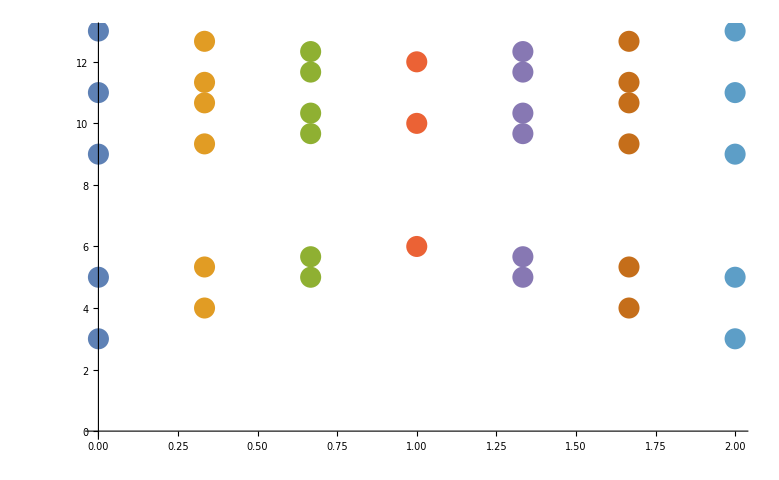

```mathematica
plotAll[TorusKnot[3,3]]
```

```mathematica
plot[BR[1,{}]]
```

-Graphics-

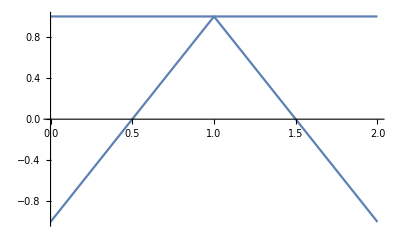

```mathematica
plot[BR[2,{1}]]
```

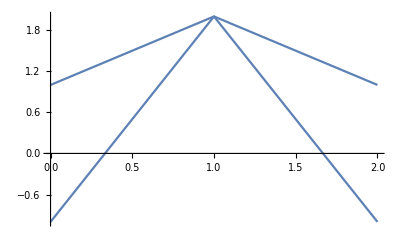

```mathematica
plot[BR[3,{1,2}]]
```

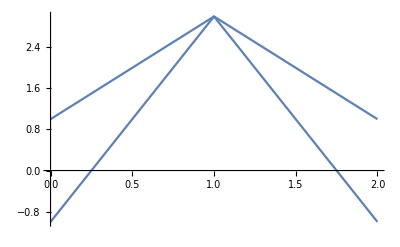

```mathematica
plot[BR[4,{1,2,3}]]
```

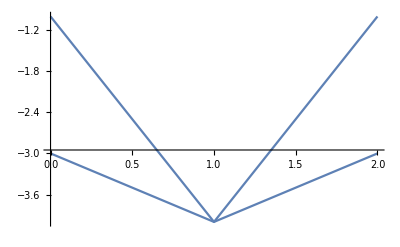

```mathematica
plot[Knot[5,2]]
```

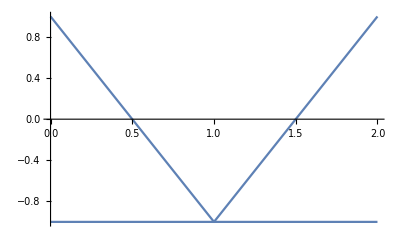

```mathematica
plot[Knot[6,1]]
```

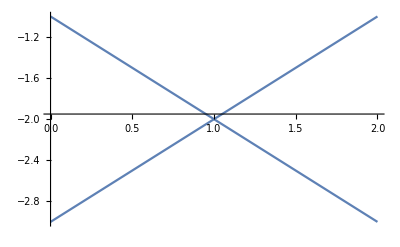

```mathematica
plot[Knot[6,2]]
```

```mathematica
plot[Knot[6,3]]
```

-Graphics-

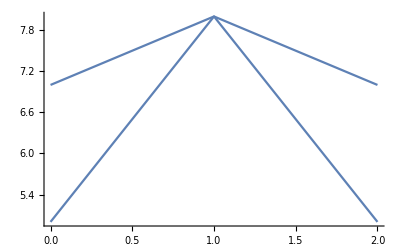

```mathematica
plot[Knot[8,19]]
```